```mathematica
URL["https://nces.ed.gov/programs/digest/d15/tables/dt15_211.60.asp"]
```

URL[https://nces.ed.gov/programs/digest/d15/tables/dt15_211.60.asp]

## Import the data

```mathematica
SetDirectory[NotebookDirectory[]]
FileNames[]
```

/Users/aarone/Desktop/teacher_salaries

{.~lock.tabn211.60.xls#,scrape.nb,tabn211.60.xls}

```mathematica
data0=Import["tabn211.60.xls","Data"][[1]]
```

{{Table 211.60. Estimated average annual salary of teachers in public elementary and secondary schools, by state: Selected years, 1969-70
              through 2014-15         ,,,,,,,,,,,,,,,},{State,Current dollars  ,,,,,,,Constant 2014-15 dollars\1\,,,,,,,},{,1969-70,1979-80,1989-90,1999-2000,2009-10,2013-14,2014-15,1969-70,1979-80,1989-90,1999-2000,2009-10,2013-14,2014-15,Percent change, 1999-2000 to
 2014-15},{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.},{   United States .............,8626.,15970.,31367.,41807.,55202.,56610.,57379.,54045.6,48686.9,58466.9,58447.9,60281.1,57022.1,57379.,-1.82876},{Alabama ....................,6818.,13060.,24828.,36689.,47571.,48720.,49497.,42717.7,39815.3,46278.5,51292.7,51947.9,49074.7,49497.,-3.50089},{Alaska ..................,10560.,27210.,43153.,46462.,59672.,65891.,66755.,66162.9,82953.7,80435.6,64955.8,65162.3,66370.7,66755.,2.76996},{Arizona .....................,8711.,15054.,29402.,36902.,46952.,45335.,45406.,54578.2,45894.3,54804.2,51590.5,51272.,45665.1,45406.,-11.9876},{Arkansas ..................,6307.,12299.,22352.,33386.,46700.,47319.,48017.,39516.1,37495.3,41663.3,46675.,50996.8,47663.5,48017.,2.87525},{California .................,10315.,18020.,37998.,47680.,68203.,71396.,72535.,64627.9,54936.6,70826.8,66658.6,74478.3,71915.8,72535.,8.81572},{,,,,,,,,,,,,,,,},{Colorado ....................,7761.,16205.,30758.,38163.,49202.,49615.,49828.,48626.,49403.3,57331.7,53353.4,53729.,49976.2,49828.,-6.60766},{Connecticut ...............,9262.,16229.,40461.,51780.,64350.,70583.,71709.,58030.4,49476.5,75417.8,72390.5,70270.8,71096.9,71709.,-0.941463},{Delaware ..................,9015.,16148.,33377.,44435.,57080.,59305.,59195.,56482.8,49229.5,62213.5,62121.9,62331.9,59736.8,59195.,-4.71158},{District of ,,,,,,,,,,,,,,,},{   Columbia ..........,10285.,22190.,38402.,47076.,64548.,73162.,75490.,64439.9,67649.5,71579.9,65814.1,70487.,73694.7,75490.,14.7018},{Florida ..................,8412.,14149.,28803.,36722.,46708.,47780.,48992.,52704.8,43135.3,53687.7,51338.8,51005.5,48127.9,48992.,-4.57127},{,,,,,,,,,,,,,,,},{Georgia .................,7276.,13853.,28006.,41023.,53112.,52924.,53382.,45587.3,42232.9,52202.1,57351.8,57998.8,53309.3,53382.,-6.92186},{Hawaii .....................,9453.,19920.,32047.,40578.,55063.,56291.,57189.,59227.1,60729.,59734.4,56729.7,60129.3,56700.8,57189.,0.809661},{Idaho ........................,6890.,13611.,23861.,35547.,46283.,44465.,45218.,43168.8,41495.1,44476.,49696.1,50541.4,44788.7,45218.,-9.01104},{Illinois .................,9569.,17601.,32794.,46486.,62077.,60124.,61083.,59953.9,53659.2,61126.8,64989.3,67788.6,60561.7,61083.,-6.01069},{Indiana ....................,8833.,15599.,30902.,41850.,49986.,50289.,50502.,55342.5,47555.8,57600.2,58508.,54585.1,50655.1,50502.,-13.6836},{,,,,,,,,,,,,,,,},{Iowa ........................,8355.,15203.,26747.,35678.,49626.,52032.,52862.,52347.7,46348.6,49855.4,49879.3,54192.,52410.8,52862.,5.97987},{Kansas .....................,7612.,13690.,28744.,34981.,46657.,48221.,48990.,47692.4,41736.,53577.7,48904.8,50949.8,48572.1,48990.,0.174114},{Kentucky .................,6953.,14520.,26292.,36380.,49543.,50560.,51093.,43563.5,44266.3,49007.3,50860.7,54101.4,50928.1,51093.,0.456721},{Louisiana ...................,7028.,13760.,24300.,33109.,48903.,49067.,47886.,44033.4,41949.4,45294.3,46287.7,53402.5,49424.2,47886.,3.45293},{Maine .....................,7572.,13071.,26881.,35561.,46106.,49232.,50017.,47441.8,39848.9,50105.2,49715.7,50348.2,49590.4,50017.,0.606019},{,,,,,,,,,,,,,,,},{Maryland ....................,9383.,17558.,36319.,44048.,63971.,64546.,64845.,58788.5,53528.1,67697.2,61580.9,69856.9,65015.9,64845.,5.30054},{Massachusetts ..............,8764.,17253.,34712.,46580.,69273.,73195.,74805.,54910.2,52598.3,64701.9,65120.7,75646.7,73727.9,74805.,14.8713},{Michigan .....................,9826.,19663.,37072.,49044.,57958.,62166.,62778.,61564.1,59945.5,69100.8,68565.5,63290.6,62618.6,62778.,-8.44082},{Minnesota ...................,8658.,15912.,32190.,39802.,52431.,54752.,56670.,54246.1,48510.1,60000.9,55644.8,57255.1,55150.6,56670.,1.8424},{Mississippi .............,5798.,11850.,24292.,31857.,45644.,42187.,42564.,36327.,36126.5,45279.4,44537.4,49843.6,42494.1,42564.,-4.43082},{,,,,,,,,,,,,,,,},{Missouri .................,7799.,13682.,27094.,35656.,45317.,46750.,47394.,48864.1,41711.6,50502.2,49848.5,49486.6,47090.4,47394.,-4.92397},{Montana .....................,7606.,14537.,25081.,32121.,45759.,49893.,50999.,47654.9,44318.2,46750.,44906.5,49969.2,50256.2,50999.,13.5672},{Nebraska ....................,7375.,13516.,25522.,33237.,46227.,49539.,50318.,46207.5,41205.5,47572.,46466.7,50480.3,49899.7,50318.,8.28838},{Nevada ....................,9215.,16295.,30590.,39390.,51524.,55813.,56703.,57735.9,49677.7,57018.6,55068.8,56264.7,56219.3,56703.,2.96754},{New Hampshire ..................,7771.,13017.,28986.,37734.,51443.,57057.,58554.,48688.6,39684.2,54028.8,52753.7,56176.2,57472.4,58554.,10.9952},{,,,,,,,,,,,,,,,},{New Jersey .................,9130.,17161.,35676.,52015.,65130.,68238.,69038.,57203.4,52317.8,66498.7,72719.1,71122.5,68734.8,69038.,-5.06204},{New Mexico .................,7796.,14887.,24756.,32554.,46258.,45727.,46003.,48845.3,45385.2,46144.2,45511.8,50514.1,46059.9,46003.,1.07927},{New York ................,10336.,19812.,38925.,51020.,71633.,76409.,77628.,64759.5,60399.8,72554.7,71328.,78223.9,76965.3,77628.,8.83241},{North Carolina ...........,7494.,14117.,27883.,39404.,46850.,44990.,47783.,46953.1,43037.7,51972.9,55088.4,51160.6,45317.5,47783.,-13.2612},{North Dakota ................,6696.,13263.,23016.,29863.,42964.,48666.,50025.,41953.3,40434.2,42901.,41749.7,46917.1,49020.3,50025.,19.8213},{,,,,,,,,,,,,,,,},{Ohio .......................,8300.,15269.,31218.,41436.,55958.,55913.,56172.,52003.1,46549.8,58189.2,57929.2,61106.6,56320.1,56172.,-3.03336},{Oklahoma ....................,6882.,13107.,23070.,31298.,47691.,44549.,44628.,43118.7,39958.6,43001.6,43755.9,52079.,44873.3,44628.,1.99318},{Oregon ......................,8818.,16266.,30840.,42336.,55224.,58638.,59811.,55248.6,49589.3,57484.6,59187.4,60305.1,59064.9,59811.,1.05354},{Pennsylvania ...............,8858.,16515.,33338.,48321.,59156.,63701.,64717.,55499.2,50348.4,62140.8,67554.7,64598.9,64164.8,64717.,-4.20061},{Rhode Island ..............,8776.,18002.,36057.,47041.,59686.,64696.,65918.,54985.4,54881.7,67208.9,65765.2,65177.6,65167.,65918.,0.232316},{,,,,,,,,,,,,,,,},{South Carolina .............,6927.,13063.,27217.,36081.,47508.,48430.,48709.,43400.6,39824.5,50731.5,50442.7,51879.1,48782.6,48709.,-3.43696},{South Dakota .............,6403.,12348.,21300.,29071.,38837.,40023.,40661.,40117.5,37644.7,39702.4,40642.4,42410.3,40314.4,40661.,#},{Tennessee ...............,7050.,13972.,27052.,36328.,46290.,47742.,48503.,44171.3,42595.7,50423.9,50788.,50549.1,48089.6,48503.,-4.49911},{Texas ....................,7255.,14132.,27496.,37567.,48261.,49690.,50576.,45455.7,43083.5,51251.5,52520.2,52701.4,50051.8,50576.,-3.70178},{Utah ....................,7644.,14909.,23686.,34946.,45885.,45695.,45848.,47892.9,45452.3,44149.8,48855.9,50106.8,46027.7,45848.,-6.15671},{,,,,,,,,,,,,,,,},{Vermont ....................,7968.,12484.,29012.,37758.,49084.,55958.,57642.,49922.9,38059.3,54077.3,52787.2,53600.2,56365.4,57642.,9.19691},{Virginia ....................,8070.,14060.,30938.,38744.,50015.,49826.,50620.,50562.,42864.,57667.3,54165.7,54616.8,50188.8,50620.,-6.54598},{Washington ..................,9225.,18820.,30457.,41043.,53003.,52969.,53714.,57798.6,57375.5,56770.7,57379.8,57879.7,53354.6,53714.,-6.38861},{West Virginia ...........,7650.,13710.,22842.,35009.,45959.,45086.,45647.,47930.5,41796.9,42576.6,48944.,50187.6,45414.2,45647.,-6.73626},{Wisconsin ................,8963.,16006.,31921.,41153.,51264.,53679.,54535.,56157.,48796.6,59499.5,57533.6,55980.7,54069.8,54535.,-5.21184},{Wyoming ...................,8232.,16012.,28141.,34127.,55861.,56583.,57715.,51577.,48814.9,52453.8,47710.9,61000.7,56995.,57715.,20.9681},{#Rounds to zero.,,,,,,,,,,,,,,,},{\1\Constant dollars based on the Consumer Price Index (CPI), prepared by the Bureau of Labor Statistics, U.S. Department of Labor, adjusted to a school-year basis. The CPI does not account for differences in inflation rates from state to state.,,,,,,,,,,,,,,,},{NOTE: Some data have been revised from previously published figures. Standard errors are not available for these estimates, which are based on state reports.,,,,,,,,,,,,,,,},{SOURCE: National Education Association, Estimates of School Statistics, 1969-70 through 2014-15. (This table was prepared September 2015.)   ,,,,,,,,,,,,,,,}}

```mathematica
Dimensions[data0]
```

{70,16}

```mathematica
data0[[;;10]]
```

{{Table 211.60. Estimated average annual salary of teachers in public elementary and secondary schools, by state: Selected years, 1969-70
              through 2014-15         ,,,,,,,,,,,,,,,},{State,Current dollars  ,,,,,,,Constant 2014-15 dollars\1\,,,,,,,},{,1969-70,1979-80,1989-90,1999-2000,2009-10,2013-14,2014-15,1969-70,1979-80,1989-90,1999-2000,2009-10,2013-14,2014-15,Percent change, 1999-2000 to
 2014-15},{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.},{   United States .............,8626.,15970.,31367.,41807.,55202.,56610.,57379.,54045.6,48686.9,58466.9,58447.9,60281.1,57022.1,57379.,-1.82876},{Alabama ....................,6818.,13060.,24828.,36689.,47571.,48720.,49497.,42717.7,39815.3,46278.5,51292.7,51947.9,49074.7,49497.,-3.50089},{Alaska ..................,10560.,27210.,43153.,46462.,59672.,65891.,66755.,66162.9,82953.7,80435.6,64955.8,65162.3,66370.7,66755.,2.76996},{Arizona .....................,8711.,15054.,29402.,36902.,46952.,45335.,45406.,54578.2,45894.3,54804.2,51590.5,51272.,45665.1,45406.,-11.9876},{Arkansas ..................,6307.,12299.,22352.,33386.,46700.,47319.,48017.,39516.1,37495.3,41663.3,46675.,50996.8,47663.5,48017.,2.87525},{California .................,10315.,18020.,37998.,47680.,68203.,71396.,72535.,64627.9,54936.6,70826.8,66658.6,74478.3,71915.8,72535.,8.81572}}

## Choose the data we want

```mathematica
data1=DeleteCases[First@SequenceCases[data0,{{"Alabama ....................",6818.,13060.,24828.,36689.,47571.,48720.,49497.,42717.69543789984,39815.32217689994,46278.45017523134,51292.70292444006,51947.94295685861,49074.70540230835,49497.,-3.500893542470037},___,{"Wyoming ...................",8232.,16012.,28141.,34127.,55861.,56583.,57715.,51577.01215089344,48814.92639330183,52453.75649996718,47710.92351119862,61000.69457259841,56994.95188380159,57715.,20.96810489625765}}],({"District of ","","","","","","","","","","","","","","",""}|{"","","","","","","","","","","","","","","",""})];
```

```mathematica
data1[[;;4]]
```

{{Alabama ....................,6818.,13060.,24828.,36689.,47571.,48720.,49497.,42717.7,39815.3,46278.5,51292.7,51947.9,49074.7,49497.,-3.50089},{Alaska ..................,10560.,27210.,43153.,46462.,59672.,65891.,66755.,66162.9,82953.7,80435.6,64955.8,65162.3,66370.7,66755.,2.76996},{Arizona .....................,8711.,15054.,29402.,36902.,46952.,45335.,45406.,54578.2,45894.3,54804.2,51590.5,51272.,45665.1,45406.,-11.9876},{Arkansas ..................,6307.,12299.,22352.,33386.,46700.,47319.,48017.,39516.1,37495.3,41663.3,46675.,50996.8,47663.5,48017.,2.87525}}

## Make an Association from the data

```mathematica
"ConstantDollars"<>#&/@{"1969-70","1979-80","1989-90","1999-2000","2009-10","2013-14","2014-15"}
```

{ConstantDollars1969-70,ConstantDollars1979-80,ConstantDollars1989-90,ConstantDollars1999-2000,ConstantDollars2009-10,ConstantDollars2013-14,ConstantDollars2014-15}

```mathematica
property={"State","CurrentDollars1969-70","CurrentDollars1979-80","CurrentDollars1989-90","CurrentDollars1999-2000","CurrentDollars2009-10","CurrentDollars2013-14","CurrentDollars2014-15","ConstantDollars1969-70","ConstantDollars1979-80","ConstantDollars1989-90","ConstantDollars1999-2000","ConstantDollars2009-10","ConstantDollars2013-14","ConstantDollars2014-15"}
```

{State,CurrentDollars1969-70,CurrentDollars1979-80,CurrentDollars1989-90,CurrentDollars1999-2000,CurrentDollars2009-10,CurrentDollars2013-14,CurrentDollars2014-15,ConstantDollars1969-70,ConstantDollars1979-80,ConstantDollars1989-90,ConstantDollars1999-2000,ConstantDollars2009-10,ConstantDollars2013-14,ConstantDollars2014-15}

```mathematica
assoc0=AssociationThread[property -> Most[#]]&/@data1;
```

## Turn states into Entity objects

```mathematica
Interpreter["AdministrativeDivision"][" District of Columbia .........."]
```

District of Columbia, United States

```mathematica
states = assoc0[[All,"State"]]
```

{Alabama ....................,Alaska ..................,Arizona .....................,Arkansas ..................,California .................,Colorado ....................,Connecticut ...............,Delaware ..................,   Columbia ..........,Florida ..................,Georgia .................,Hawaii .....................,Idaho ........................,Illinois .................,Indiana ....................,Iowa ........................,Kansas .....................,Kentucky .................,Louisiana ...................,Maine .....................,Maryland ....................,Massachusetts ..............,Michigan .....................,Minnesota ...................,Mississippi .............,Missouri .................,Montana .....................,Nebraska ....................,Nevada ....................,New Hampshire ..................,New Jersey .................,New Mexico .................,New York ................,North Carolina ...........,North Dakota ................,Ohio .......................,Oklahoma ....................,Oregon ......................,Pennsylvania ...............,Rhode Island ..............,South Carolina .............,South Dakota .............,Tennessee ...............,Texas ....................,Utah ....................,Vermont ....................,Virginia ....................,Washington ..................,West Virginia ...........,Wisconsin ................,Wyoming ...................}

```mathematica
Replace[StringTrim/@StringReplace[states,"." -> ""],"Columbia" -> "District of Columbia",{1}]
```

{Alabama,Alaska,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,District of Columbia,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Iowa,Kansas,Kentucky,Louisiana,Maine,Maryland,Massachusetts,Michigan,Minnesota,Mississippi,Missouri,Montana,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oklahoma,Oregon,Pennsylvania,Rhode Island,South Carolina,South Dakota,Tennessee,Texas,Utah,Vermont,Virginia,Washington,West Virginia,Wisconsin,Wyoming}

```mathematica
stateassoc = AssociationThread[states-> Interpreter["AdministrativeDivision"][Replace[StringTrim/@StringReplace[states,"." -> ""],"Columbia" -> "District of Columbia",{1}]]];
```

```mathematica
stateassoc
```

<|Alabama ....................→Alabama, United States,Alaska ..................→Alaska, United States,Arizona .....................→Arizona, United States,Arkansas ..................→Arkansas, United States,California .................→California, United States,Colorado ....................→Colorado, United States,Connecticut ...............→Connecticut, United States,Delaware ..................→Delaware, United States,   Columbia ..........→District of Columbia, United States,Florida ..................→Florida, United States,Georgia .................→Georgia, United States,Hawaii .....................→Hawaii, United States,Idaho ........................→Idaho, United States,Illinois .................→Illinois, United States,Indiana ....................→Indiana, United States,Iowa ........................→Iowa, United States,Kansas .....................→Kansas, United States,Kentucky .................→Kentucky, United States,Louisiana ...................→Louisiana, United States,Maine .....................→Maine, United States,Maryland ....................→Maryland, United States,Massachusetts ..............→Massachusetts, United States,Michigan .....................→Michigan, United States,Minnesota ...................→Minnesota, United States,Mississippi .............→Mississippi, United States,Missouri .................→Missouri, United States,Montana .....................→Montana, United States,Nebraska ....................→Nebraska, United States,Nevada ....................→Nevada, United States,New Hampshire ..................→New Hampshire, United States,New Jersey .................→New Jersey, United States,New Mexico .................→New Mexico, United States,New York ................→New York, United States,North Carolina ...........→North Carolina, United States,North Dakota ................→North Dakota, United States,Ohio .......................→Ohio, United States,Oklahoma ....................→Oklahoma, United States,Oregon ......................→Oregon, United States,Pennsylvania ...............→Pennsylvania, United States,Rhode Island ..............→Rhode Island, United States,South Carolina .............→South Carolina, United States,South Dakota .............→South Dakota, United States,Tennessee ...............→Tennessee, United States,Texas ....................→Texas, United States,Utah ....................→Utah, United States,Vermont ....................→Vermont, United States,Virginia ....................→Virginia, United States,Washington ..................→Washington, United States,West Virginia ...........→West Virginia, United States,Wisconsin ................→Wisconsin, United States,Wyoming ...................→Wyoming, United States|>

```mathematica
assoc0
```

{<|State→Alabama ....................,CurrentDollars1969-70→6818.,CurrentDollars1979-80→13060.,CurrentDollars1989-90→24828.,CurrentDollars1999-2000→36689.,CurrentDollars2009-10→47571.,CurrentDollars2013-14→48720.,CurrentDollars2014-15→49497.,ConstantDollars1969-70→42717.7,ConstantDollars1979-80→39815.3,ConstantDollars1989-90→46278.5,ConstantDollars1999-2000→51292.7,ConstantDollars2009-10→51947.9,ConstantDollars2013-14→49074.7,ConstantDollars2014-15→49497.|>,<|State→Alaska ..................,CurrentDollars1969-70→10560.,CurrentDollars1979-80→27210.,CurrentDollars1989-90→43153.,CurrentDollars1999-2000→46462.,CurrentDollars2009-10→59672.,CurrentDollars2013-14→65891.,CurrentDollars2014-15→66755.,ConstantDollars1969-70→66162.9,ConstantDollars1979-80→82953.7,ConstantDollars1989-90→80435.6,ConstantDollars1999-2000→64955.8,ConstantDollars2009-10→65162.3,ConstantDollars2013-14→66370.7,ConstantDollars2014-15→66755.|>,<|State→Arizona .....................,CurrentDollars1969-70→8711.,CurrentDollars1979-80→15054.,CurrentDollars1989-90→29402.,CurrentDollars1999-2000→36902.,CurrentDollars2009-10→46952.,CurrentDollars2013-14→45335.,CurrentDollars2014-15→45406.,ConstantDollars1969-70→54578.2,ConstantDollars1979-80→45894.3,ConstantDollars1989-90→54804.2,ConstantDollars1999-2000→51590.5,ConstantDollars2009-10→51272.,ConstantDollars2013-14→45665.1,ConstantDollars2014-15→45406.|>,<|State→Arkansas ..................,CurrentDollars1969-70→6307.,CurrentDollars1979-80→12299.,CurrentDollars1989-90→22352.,CurrentDollars1999-2000→33386.,CurrentDollars2009-10→46700.,CurrentDollars2013-14→47319.,CurrentDollars2014-15→48017.,ConstantDollars1969-70→39516.1,ConstantDollars1979-80→37495.3,ConstantDollars1989-90→41663.3,ConstantDollars1999-2000→46675.,ConstantDollars2009-10→50996.8,ConstantDollars2013-14→47663.5,ConstantDollars2014-15→48017.|>,<|State→California .................,CurrentDollars1969-70→10315.,CurrentDollars1979-80→18020.,CurrentDollars1989-90→37998.,CurrentDollars1999-2000→47680.,CurrentDollars2009-10→68203.,CurrentDollars2013-14→71396.,CurrentDollars2014-15→72535.,ConstantDollars1969-70→64627.9,ConstantDollars1979-80→54936.6,ConstantDollars1989-90→70826.8,ConstantDollars1999-2000→66658.6,ConstantDollars2009-10→74478.3,ConstantDollars2013-14→71915.8,ConstantDollars2014-15→72535.|>,<|State→Colorado ....................,CurrentDollars1969-70→7761.,CurrentDollars1979-80→16205.,CurrentDollars1989-90→30758.,CurrentDollars1999-2000→38163.,CurrentDollars2009-10→49202.,CurrentDollars2013-14→49615.,CurrentDollars2014-15→49828.,ConstantDollars1969-70→48626.,ConstantDollars1979-80→49403.3,ConstantDollars1989-90→57331.7,ConstantDollars1999-2000→53353.4,ConstantDollars2009-10→53729.,ConstantDollars2013-14→49976.2,ConstantDollars2014-15→49828.|>,<|State→Connecticut ...............,CurrentDollars1969-70→9262.,CurrentDollars1979-80→16229.,CurrentDollars1989-90→40461.,CurrentDollars1999-2000→51780.,CurrentDollars2009-10→64350.,CurrentDollars2013-14→70583.,CurrentDollars2014-15→71709.,ConstantDollars1969-70→58030.4,ConstantDollars1979-80→49476.5,ConstantDollars1989-90→75417.8,ConstantDollars1999-2000→72390.5,ConstantDollars2009-10→70270.8,ConstantDollars2013-14→71096.9,ConstantDollars2014-15→71709.|>,<|State→Delaware ..................,CurrentDollars1969-70→9015.,CurrentDollars1979-80→16148.,CurrentDollars1989-90→33377.,CurrentDollars1999-2000→44435.,CurrentDollars2009-10→57080.,CurrentDollars2013-14→59305.,CurrentDollars2014-15→59195.,ConstantDollars1969-70→56482.8,ConstantDollars1979-80→49229.5,ConstantDollars1989-90→62213.5,ConstantDollars1999-2000→62121.9,ConstantDollars2009-10→62331.9,ConstantDollars2013-14→59736.8,ConstantDollars2014-15→59195.|>,<|State→   Columbia ..........,CurrentDollars1969-70→10285.,CurrentDollars1979-80→22190.,CurrentDollars1989-90→38402.,CurrentDollars1999-2000→47076.,CurrentDollars2009-10→64548.,CurrentDollars2013-14→73162.,CurrentDollars2014-15→75490.,ConstantDollars1969-70→64439.9,ConstantDollars1979-80→67649.5,ConstantDollars1989-90→71579.9,ConstantDollars1999-2000→65814.1,ConstantDollars2009-10→70487.,ConstantDollars2013-14→73694.7,ConstantDollars2014-15→75490.|>,<|State→Florida ..................,CurrentDollars1969-70→8412.,CurrentDollars1979-80→14149.,CurrentDollars1989-90→28803.,CurrentDollars1999-2000→36722.,CurrentDollars2009-10→46708.,CurrentDollars2013-14→47780.,CurrentDollars2014-15→48992.,ConstantDollars1969-70→52704.8,ConstantDollars1979-80→43135.3,ConstantDollars1989-90→53687.7,ConstantDollars1999-2000→51338.8,ConstantDollars2009-10→51005.5,ConstantDollars2013-14→48127.9,ConstantDollars2014-15→48992.|>,<|State→Georgia .................,CurrentDollars1969-70→7276.,CurrentDollars1979-80→13853.,CurrentDollars1989-90→28006.,CurrentDollars1999-2000→41023.,CurrentDollars2009-10→53112.,CurrentDollars2013-14→52924.,CurrentDollars2014-15→53382.,ConstantDollars1969-70→45587.3,ConstantDollars1979-80→42232.9,ConstantDollars1989-90→52202.1,ConstantDollars1999-2000→57351.8,ConstantDollars2009-10→57998.8,ConstantDollars2013-14→53309.3,ConstantDollars2014-15→53382.|>,<|State→Hawaii .....................,CurrentDollars1969-70→9453.,CurrentDollars1979-80→19920.,CurrentDollars1989-90→32047.,CurrentDollars1999-2000→40578.,CurrentDollars2009-10→55063.,CurrentDollars2013-14→56291.,CurrentDollars2014-15→57189.,ConstantDollars1969-70→59227.1,ConstantDollars1979-80→60729.,ConstantDollars1989-90→59734.4,ConstantDollars1999-2000→56729.7,ConstantDollars2009-10→60129.3,ConstantDollars2013-14→56700.8,ConstantDollars2014-15→57189.|>,<|State→Idaho ........................,CurrentDollars1969-70→6890.,CurrentDollars1979-80→13611.,CurrentDollars1989-90→23861.,CurrentDollars1999-2000→35547.,CurrentDollars2009-10→46283.,CurrentDollars2013-14→44465.,CurrentDollars2014-15→45218.,ConstantDollars1969-70→43168.8,ConstantDollars1979-80→41495.1,ConstantDollars1989-90→44476.,ConstantDollars1999-2000→49696.1,ConstantDollars2009-10→50541.4,ConstantDollars2013-14→44788.7,ConstantDollars2014-15→45218.|>,<|State→Illinois .................,CurrentDollars1969-70→9569.,CurrentDollars1979-80→17601.,CurrentDollars1989-90→32794.,CurrentDollars1999-2000→46486.,CurrentDollars2009-10→62077.,CurrentDollars2013-14→60124.,CurrentDollars2014-15→61083.,ConstantDollars1969-70→59953.9,ConstantDollars1979-80→53659.2,ConstantDollars1989-90→61126.8,ConstantDollars1999-2000→64989.3,ConstantDollars2009-10→67788.6,ConstantDollars2013-14→60561.7,ConstantDollars2014-15→61083.|>,<|State→Indiana ....................,CurrentDollars1969-70→8833.,CurrentDollars1979-80→15599.,CurrentDollars1989-90→30902.,CurrentDollars1999-2000→41850.,CurrentDollars2009-10→49986.,CurrentDollars2013-14→50289.,CurrentDollars2014-15→50502.,ConstantDollars1969-70→55342.5,ConstantDollars1979-80→47555.8,ConstantDollars1989-90→57600.2,ConstantDollars1999-2000→58508.,ConstantDollars2009-10→54585.1,ConstantDollars2013-14→50655.1,ConstantDollars2014-15→50502.|>,<|State→Iowa ........................,CurrentDollars1969-70→8355.,CurrentDollars1979-80→15203.,CurrentDollars1989-90→26747.,CurrentDollars1999-2000→35678.,CurrentDollars2009-10→49626.,CurrentDollars2013-14→52032.,CurrentDollars2014-15→52862.,ConstantDollars1969-70→52347.7,ConstantDollars1979-80→46348.6,ConstantDollars1989-90→49855.4,ConstantDollars1999-2000→49879.3,ConstantDollars2009-10→54192.,ConstantDollars2013-14→52410.8,ConstantDollars2014-15→52862.|>,<|State→Kansas .....................,CurrentDollars1969-70→7612.,CurrentDollars1979-80→13690.,CurrentDollars1989-90→28744.,CurrentDollars1999-2000→34981.,CurrentDollars2009-10→46657.,CurrentDollars2013-14→48221.,CurrentDollars2014-15→48990.,ConstantDollars1969-70→47692.4,ConstantDollars1979-80→41736.,ConstantDollars1989-90→53577.7,ConstantDollars1999-2000→48904.8,ConstantDollars2009-10→50949.8,ConstantDollars2013-14→48572.1,ConstantDollars2014-15→48990.|>,<|State→Kentucky .................,CurrentDollars1969-70→6953.,CurrentDollars1979-80→14520.,CurrentDollars1989-90→26292.,CurrentDollars1999-2000→36380.,CurrentDollars2009-10→49543.,CurrentDollars2013-14→50560.,CurrentDollars2014-15→51093.,ConstantDollars1969-70→43563.5,ConstantDollars1979-80→44266.3,ConstantDollars1989-90→49007.3,ConstantDollars1999-2000→50860.7,ConstantDollars2009-10→54101.4,ConstantDollars2013-14→50928.1,ConstantDollars2014-15→51093.|>,<|State→Louisiana ...................,CurrentDollars1969-70→7028.,CurrentDollars1979-80→13760.,CurrentDollars1989-90→24300.,CurrentDollars1999-2000→33109.,CurrentDollars2009-10→48903.,CurrentDollars2013-14→49067.,CurrentDollars2014-15→47886.,ConstantDollars1969-70→44033.4,ConstantDollars1979-80→41949.4,ConstantDollars1989-90→45294.3,ConstantDollars1999-2000→46287.7,ConstantDollars2009-10→53402.5,ConstantDollars2013-14→49424.2,ConstantDollars2014-15→47886.|>,<|State→Maine .....................,CurrentDollars1969-70→7572.,CurrentDollars1979-80→13071.,CurrentDollars1989-90→26881.,CurrentDollars1999-2000→35561.,CurrentDollars2009-10→46106.,CurrentDollars2013-14→49232.,CurrentDollars2014-15→50017.,ConstantDollars1969-70→47441.8,ConstantDollars1979-80→39848.9,ConstantDollars1989-90→50105.2,ConstantDollars1999-2000→49715.7,ConstantDollars2009-10→50348.2,ConstantDollars2013-14→49590.4,ConstantDollars2014-15→50017.|>,<|State→Maryland ....................,CurrentDollars1969-70→9383.,CurrentDollars1979-80→17558.,CurrentDollars1989-90→36319.,CurrentDollars1999-2000→44048.,CurrentDollars2009-10→63971.,CurrentDollars2013-14→64546.,CurrentDollars2014-15→64845.,ConstantDollars1969-70→58788.5,ConstantDollars1979-80→53528.1,ConstantDollars1989-90→67697.2,ConstantDollars1999-2000→61580.9,ConstantDollars2009-10→69856.9,ConstantDollars2013-14→65015.9,ConstantDollars2014-15→64845.|>,<|State→Massachusetts ..............,CurrentDollars1969-70→8764.,CurrentDollars1979-80→17253.,CurrentDollars1989-90→34712.,CurrentDollars1999-2000→46580.,CurrentDollars2009-10→69273.,CurrentDollars2013-14→73195.,CurrentDollars2014-15→74805.,ConstantDollars1969-70→54910.2,ConstantDollars1979-80→52598.3,ConstantDollars1989-90→64701.9,ConstantDollars1999-2000→65120.7,ConstantDollars2009-10→75646.7,ConstantDollars2013-14→73727.9,ConstantDollars2014-15→74805.|>,<|State→Michigan .....................,CurrentDollars1969-70→9826.,CurrentDollars1979-80→19663.,CurrentDollars1989-90→37072.,CurrentDollars1999-2000→49044.,CurrentDollars2009-10→57958.,CurrentDollars2013-14→62166.,CurrentDollars2014-15→62778.,ConstantDollars1969-70→61564.1,ConstantDollars1979-80→59945.5,ConstantDollars1989-90→69100.8,ConstantDollars1999-2000→68565.5,ConstantDollars2009-10→63290.6,ConstantDollars2013-14→62618.6,ConstantDollars2014-15→62778.|>,<|State→Minnesota ...................,CurrentDollars1969-70→8658.,CurrentDollars1979-80→15912.,CurrentDollars1989-90→32190.,CurrentDollars1999-2000→39802.,CurrentDollars2009-10→52431.,CurrentDollars2013-14→54752.,CurrentDollars2014-15→56670.,ConstantDollars1969-70→54246.1,ConstantDollars1979-80→48510.1,ConstantDollars1989-90→60000.9,ConstantDollars1999-2000→55644.8,ConstantDollars2009-10→57255.1,ConstantDollars2013-14→55150.6,ConstantDollars2014-15→56670.|>,<|State→Mississippi .............,CurrentDollars1969-70→5798.,CurrentDollars1979-80→11850.,CurrentDollars1989-90→24292.,CurrentDollars1999-2000→31857.,CurrentDollars2009-10→45644.,CurrentDollars2013-14→42187.,CurrentDollars2014-15→42564.,ConstantDollars1969-70→36327.,ConstantDollars1979-80→36126.5,ConstantDollars1989-90→45279.4,ConstantDollars1999-2000→44537.4,ConstantDollars2009-10→49843.6,ConstantDollars2013-14→42494.1,ConstantDollars2014-15→42564.|>,<|State→Missouri .................,CurrentDollars1969-70→7799.,CurrentDollars1979-80→13682.,CurrentDollars1989-90→27094.,CurrentDollars1999-2000→35656.,CurrentDollars2009-10→45317.,CurrentDollars2013-14→46750.,CurrentDollars2014-15→47394.,ConstantDollars1969-70→48864.1,ConstantDollars1979-80→41711.6,ConstantDollars1989-90→50502.2,ConstantDollars1999-2000→49848.5,ConstantDollars2009-10→49486.6,ConstantDollars2013-14→47090.4,ConstantDollars2014-15→47394.|>,<|State→Montana .....................,CurrentDollars1969-70→7606.,CurrentDollars1979-80→14537.,CurrentDollars1989-90→25081.,CurrentDollars1999-2000→32121.,CurrentDollars2009-10→45759.,CurrentDollars2013-14→49893.,CurrentDollars2014-15→50999.,ConstantDollars1969-70→47654.9,ConstantDollars1979-80→44318.2,ConstantDollars1989-90→46750.,ConstantDollars1999-2000→44906.5,ConstantDollars2009-10→49969.2,ConstantDollars2013-14→50256.2,ConstantDollars2014-15→50999.|>,<|State→Nebraska ....................,CurrentDollars1969-70→7375.,CurrentDollars1979-80→13516.,CurrentDollars1989-90→25522.,CurrentDollars1999-2000→33237.,CurrentDollars2009-10→46227.,CurrentDollars2013-14→49539.,CurrentDollars2014-15→50318.,ConstantDollars1969-70→46207.5,ConstantDollars1979-80→41205.5,ConstantDollars1989-90→47572.,ConstantDollars1999-2000→46466.7,ConstantDollars2009-10→50480.3,ConstantDollars2013-14→49899.7,ConstantDollars2014-15→50318.|>,<|State→Nevada ....................,CurrentDollars1969-70→9215.,CurrentDollars1979-80→16295.,CurrentDollars1989-90→30590.,CurrentDollars1999-2000→39390.,CurrentDollars2009-10→51524.,CurrentDollars2013-14→55813.,CurrentDollars2014-15→56703.,ConstantDollars1969-70→57735.9,ConstantDollars1979-80→49677.7,ConstantDollars1989-90→57018.6,ConstantDollars1999-2000→55068.8,ConstantDollars2009-10→56264.7,ConstantDollars2013-14→56219.3,ConstantDollars2014-15→56703.|>,<|State→New Hampshire ..................,CurrentDollars1969-70→7771.,CurrentDollars1979-80→13017.,CurrentDollars1989-90→28986.,CurrentDollars1999-2000→37734.,CurrentDollars2009-10→51443.,CurrentDollars2013-14→57057.,CurrentDollars2014-15→58554.,ConstantDollars1969-70→48688.6,ConstantDollars1979-80→39684.2,ConstantDollars1989-90→54028.8,ConstantDollars1999-2000→52753.7,ConstantDollars2009-10→56176.2,ConstantDollars2013-14→57472.4,ConstantDollars2014-15→58554.|>,<|State→New Jersey .................,CurrentDollars1969-70→9130.,CurrentDollars1979-80→17161.,CurrentDollars1989-90→35676.,CurrentDollars1999-2000→52015.,CurrentDollars2009-10→65130.,CurrentDollars2013-14→68238.,CurrentDollars2014-15→69038.,ConstantDollars1969-70→57203.4,ConstantDollars1979-80→52317.8,ConstantDollars1989-90→66498.7,ConstantDollars1999-2000→72719.1,ConstantDollars2009-10→71122.5,ConstantDollars2013-14→68734.8,ConstantDollars2014-15→69038.|>,<|State→New Mexico .................,CurrentDollars1969-70→7796.,CurrentDollars1979-80→14887.,CurrentDollars1989-90→24756.,CurrentDollars1999-2000→32554.,CurrentDollars2009-10→46258.,CurrentDollars2013-14→45727.,CurrentDollars2014-15→46003.,ConstantDollars1969-70→48845.3,ConstantDollars1979-80→45385.2,ConstantDollars1989-90→46144.2,ConstantDollars1999-2000→45511.8,ConstantDollars2009-10→50514.1,ConstantDollars2013-14→46059.9,ConstantDollars2014-15→46003.|>,<|State→New York ................,CurrentDollars1969-70→10336.,CurrentDollars1979-80→19812.,CurrentDollars1989-90→38925.,CurrentDollars1999-2000→51020.,CurrentDollars2009-10→71633.,CurrentDollars2013-14→76409.,CurrentDollars2014-15→77628.,ConstantDollars1969-70→64759.5,ConstantDollars1979-80→60399.8,ConstantDollars1989-90→72554.7,ConstantDollars1999-2000→71328.,ConstantDollars2009-10→78223.9,ConstantDollars2013-14→76965.3,ConstantDollars2014-15→77628.|>,<|State→North Carolina ...........,CurrentDollars1969-70→7494.,CurrentDollars1979-80→14117.,CurrentDollars1989-90→27883.,CurrentDollars1999-2000→39404.,CurrentDollars2009-10→46850.,CurrentDollars2013-14→44990.,CurrentDollars2014-15→47783.,ConstantDollars1969-70→46953.1,ConstantDollars1979-80→43037.7,ConstantDollars1989-90→51972.9,ConstantDollars1999-2000→55088.4,ConstantDollars2009-10→51160.6,ConstantDollars2013-14→45317.5,ConstantDollars2014-15→47783.|>,<|State→North Dakota ................,CurrentDollars1969-70→6696.,CurrentDollars1979-80→13263.,CurrentDollars1989-90→23016.,CurrentDollars1999-2000→29863.,CurrentDollars2009-10→42964.,CurrentDollars2013-14→48666.,CurrentDollars2014-15→50025.,ConstantDollars1969-70→41953.3,ConstantDollars1979-80→40434.2,ConstantDollars1989-90→42901.,ConstantDollars1999-2000→41749.7,ConstantDollars2009-10→46917.1,ConstantDollars2013-14→49020.3,ConstantDollars2014-15→50025.|>,<|State→Ohio .......................,CurrentDollars1969-70→8300.,CurrentDollars1979-80→15269.,CurrentDollars1989-90→31218.,CurrentDollars1999-2000→41436.,CurrentDollars2009-10→55958.,CurrentDollars2013-14→55913.,CurrentDollars2014-15→56172.,ConstantDollars1969-70→52003.1,ConstantDollars1979-80→46549.8,ConstantDollars1989-90→58189.2,ConstantDollars1999-2000→57929.2,ConstantDollars2009-10→61106.6,ConstantDollars2013-14→56320.1,ConstantDollars2014-15→56172.|>,<|State→Oklahoma ....................,CurrentDollars1969-70→6882.,CurrentDollars1979-80→13107.,CurrentDollars1989-90→23070.,CurrentDollars1999-2000→31298.,CurrentDollars2009-10→47691.,CurrentDollars2013-14→44549.,CurrentDollars2014-15→44628.,ConstantDollars1969-70→43118.7,ConstantDollars1979-80→39958.6,ConstantDollars1989-90→43001.6,ConstantDollars1999-2000→43755.9,ConstantDollars2009-10→52079.,ConstantDollars2013-14→44873.3,ConstantDollars2014-15→44628.|>,<|State→Oregon ......................,CurrentDollars1969-70→8818.,CurrentDollars1979-80→16266.,CurrentDollars1989-90→30840.,CurrentDollars1999-2000→42336.,CurrentDollars2009-10→55224.,CurrentDollars2013-14→58638.,CurrentDollars2014-15→59811.,ConstantDollars1969-70→55248.6,ConstantDollars1979-80→49589.3,ConstantDollars1989-90→57484.6,ConstantDollars1999-2000→59187.4,ConstantDollars2009-10→60305.1,ConstantDollars2013-14→59064.9,ConstantDollars2014-15→59811.|>,<|State→Pennsylvania ...............,CurrentDollars1969-70→8858.,CurrentDollars1979-80→16515.,CurrentDollars1989-90→33338.,CurrentDollars1999-2000→48321.,CurrentDollars2009-10→59156.,CurrentDollars2013-14→63701.,CurrentDollars2014-15→64717.,ConstantDollars1969-70→55499.2,ConstantDollars1979-80→50348.4,ConstantDollars1989-90→62140.8,ConstantDollars1999-2000→67554.7,ConstantDollars2009-10→64598.9,ConstantDollars2013-14→64164.8,ConstantDollars2014-15→64717.|>,<|State→Rhode Island ..............,CurrentDollars1969-70→8776.,CurrentDollars1979-80→18002.,CurrentDollars1989-90→36057.,CurrentDollars1999-2000→47041.,CurrentDollars2009-10→59686.,CurrentDollars2013-14→64696.,CurrentDollars2014-15→65918.,ConstantDollars1969-70→54985.4,ConstantDollars1979-80→54881.7,ConstantDollars1989-90→67208.9,ConstantDollars1999-2000→65765.2,ConstantDollars2009-10→65177.6,ConstantDollars2013-14→65167.,ConstantDollars2014-15→65918.|>,<|State→South Carolina .............,CurrentDollars1969-70→6927.,CurrentDollars1979-80→13063.,CurrentDollars1989-90→27217.,CurrentDollars1999-2000→36081.,CurrentDollars2009-10→47508.,CurrentDollars2013-14→48430.,CurrentDollars2014-15→48709.,ConstantDollars1969-70→43400.6,ConstantDollars1979-80→39824.5,ConstantDollars1989-90→50731.5,ConstantDollars1999-2000→50442.7,ConstantDollars2009-10→51879.1,ConstantDollars2013-14→48782.6,ConstantDollars2014-15→48709.|>,<|State→South Dakota .............,CurrentDollars1969-70→6403.,CurrentDollars1979-80→12348.,CurrentDollars1989-90→21300.,CurrentDollars1999-2000→29071.,CurrentDollars2009-10→38837.,CurrentDollars2013-14→40023.,CurrentDollars2014-15→40661.,ConstantDollars1969-70→40117.5,ConstantDollars1979-80→37644.7,ConstantDollars1989-90→39702.4,ConstantDollars1999-2000→40642.4,ConstantDollars2009-10→42410.3,ConstantDollars2013-14→40314.4,ConstantDollars2014-15→40661.|>,<|State→Tennessee ...............,CurrentDollars1969-70→7050.,CurrentDollars1979-80→13972.,CurrentDollars1989-90→27052.,CurrentDollars1999-2000→36328.,CurrentDollars2009-10→46290.,CurrentDollars2013-14→47742.,CurrentDollars2014-15→48503.,ConstantDollars1969-70→44171.3,ConstantDollars1979-80→42595.7,ConstantDollars1989-90→50423.9,ConstantDollars1999-2000→50788.,ConstantDollars2009-10→50549.1,ConstantDollars2013-14→48089.6,ConstantDollars2014-15→48503.|>,<|State→Texas ....................,CurrentDollars1969-70→7255.,CurrentDollars1979-80→14132.,CurrentDollars1989-90→27496.,CurrentDollars1999-2000→37567.,CurrentDollars2009-10→48261.,CurrentDollars2013-14→49690.,CurrentDollars2014-15→50576.,ConstantDollars1969-70→45455.7,ConstantDollars1979-80→43083.5,ConstantDollars1989-90→51251.5,ConstantDollars1999-2000→52520.2,ConstantDollars2009-10→52701.4,ConstantDollars2013-14→50051.8,ConstantDollars2014-15→50576.|>,<|State→Utah ....................,CurrentDollars1969-70→7644.,CurrentDollars1979-80→14909.,CurrentDollars1989-90→23686.,CurrentDollars1999-2000→34946.,CurrentDollars2009-10→45885.,CurrentDollars2013-14→45695.,CurrentDollars2014-15→45848.,ConstantDollars1969-70→47892.9,ConstantDollars1979-80→45452.3,ConstantDollars1989-90→44149.8,ConstantDollars1999-2000→48855.9,ConstantDollars2009-10→50106.8,ConstantDollars2013-14→46027.7,ConstantDollars2014-15→45848.|>,<|State→Vermont ....................,CurrentDollars1969-70→7968.,CurrentDollars1979-80→12484.,CurrentDollars1989-90→29012.,CurrentDollars1999-2000→37758.,CurrentDollars2009-10→49084.,CurrentDollars2013-14→55958.,CurrentDollars2014-15→57642.,ConstantDollars1969-70→49922.9,ConstantDollars1979-80→38059.3,ConstantDollars1989-90→54077.3,ConstantDollars1999-2000→52787.2,ConstantDollars2009-10→53600.2,ConstantDollars2013-14→56365.4,ConstantDollars2014-15→57642.|>,<|State→Virginia ....................,CurrentDollars1969-70→8070.,CurrentDollars1979-80→14060.,CurrentDollars1989-90→30938.,CurrentDollars1999-2000→38744.,CurrentDollars2009-10→50015.,CurrentDollars2013-14→49826.,CurrentDollars2014-15→50620.,ConstantDollars1969-70→50562.,ConstantDollars1979-80→42864.,ConstantDollars1989-90→57667.3,ConstantDollars1999-2000→54165.7,ConstantDollars2009-10→54616.8,ConstantDollars2013-14→50188.8,ConstantDollars2014-15→50620.|>,<|State→Washington ..................,CurrentDollars1969-70→9225.,CurrentDollars1979-80→18820.,CurrentDollars1989-90→30457.,CurrentDollars1999-2000→41043.,CurrentDollars2009-10→53003.,CurrentDollars2013-14→52969.,CurrentDollars2014-15→53714.,ConstantDollars1969-70→57798.6,ConstantDollars1979-80→57375.5,ConstantDollars1989-90→56770.7,ConstantDollars1999-2000→57379.8,ConstantDollars2009-10→57879.7,ConstantDollars2013-14→53354.6,ConstantDollars2014-15→53714.|>,<|State→West Virginia ...........,CurrentDollars1969-70→7650.,CurrentDollars1979-80→13710.,CurrentDollars1989-90→22842.,CurrentDollars1999-2000→35009.,CurrentDollars2009-10→45959.,CurrentDollars2013-14→45086.,CurrentDollars2014-15→45647.,ConstantDollars1969-70→47930.5,ConstantDollars1979-80→41796.9,ConstantDollars1989-90→42576.6,ConstantDollars1999-2000→48944.,ConstantDollars2009-10→50187.6,ConstantDollars2013-14→45414.2,ConstantDollars2014-15→45647.|>,<|State→Wisconsin ................,CurrentDollars1969-70→8963.,CurrentDollars1979-80→16006.,CurrentDollars1989-90→31921.,CurrentDollars1999-2000→41153.,CurrentDollars2009-10→51264.,CurrentDollars2013-14→53679.,CurrentDollars2014-15→54535.,ConstantDollars1969-70→56157.,ConstantDollars1979-80→48796.6,ConstantDollars1989-90→59499.5,ConstantDollars1999-2000→57533.6,ConstantDollars2009-10→55980.7,ConstantDollars2013-14→54069.8,ConstantDollars2014-15→54535.|>,<|State→Wyoming ...................,CurrentDollars1969-70→8232.,CurrentDollars1979-80→16012.,CurrentDollars1989-90→28141.,CurrentDollars1999-2000→34127.,CurrentDollars2009-10→55861.,CurrentDollars2013-14→56583.,CurrentDollars2014-15→57715.,ConstantDollars1969-70→51577.,ConstantDollars1979-80→48814.9,ConstantDollars1989-90→52453.8,ConstantDollars1999-2000→47710.9,ConstantDollars2009-10→61000.7,ConstantDollars2013-14→56995.,ConstantDollars2014-15→57715.|>}

```mathematica
assoc1=Module[{rec = #},
rec["State"] = stateassoc[rec["State"]];
rec]&/@assoc0;
```

## Construct TimeSeries

```mathematica
RandomChoice[assoc1]
```

<|State→South Dakota, United States,CurrentDollars1969-70→6403.,CurrentDollars1979-80→12348.,CurrentDollars1989-90→21300.,CurrentDollars1999-2000→29071.,CurrentDollars2009-10→38837.,CurrentDollars2013-14→40023.,CurrentDollars2014-15→40661.,ConstantDollars1969-70→40117.5,ConstantDollars1979-80→37644.7,ConstantDollars1989-90→39702.4,ConstantDollars1999-2000→40642.4,ConstantDollars2009-10→42410.3,ConstantDollars2013-14→40314.4,ConstantDollars2014-15→40661.|>

```mathematica
curprops=First/@{"CurrentDollars1969-70"->6403.,"CurrentDollars1979-80"->12348.,"CurrentDollars1989-90"->21300.,"CurrentDollars1999-2000"->29071.,"CurrentDollars2009-10"->38837.,"CurrentDollars2013-14"->40023.,"CurrentDollars2014-15"->40661.}
```

{CurrentDollars1969-70,CurrentDollars1979-80,CurrentDollars1989-90,CurrentDollars1999-2000,CurrentDollars2009-10,CurrentDollars2013-14,CurrentDollars2014-15}

```mathematica
constprops=First/@{"ConstantDollars1969-70"->40117.5423714979,"ConstantDollars1979-80"->37644.6859295835,"ConstantDollars1989-90"->39702.39200630045,"ConstantDollars1999-2000"->40642.4314294856,"ConstantDollars2009-10"->42410.33950548691,"ConstantDollars2013-14"->40314.386993361804,"ConstantDollars2014-15"->40661.}
```

{ConstantDollars1969-70,ConstantDollars1979-80,ConstantDollars1989-90,ConstantDollars1999-2000,ConstantDollars2009-10,ConstantDollars2013-14,ConstantDollars2014-15}

```mathematica
{{date,value},{date2,value2}...}
```

```mathematica
assoc2=Module[{rec=#},

rec["AverageTeacherSalaryCurrentDollars"] =
TimeSeries[{DateObject@StringReplace[#,{"CurrentDollars","-"~~___}->""],
Quantity[rec[#],"USDollars"]}&/@curprops];

rec["AverageTeacherSalaryConstantDollars"] =
TimeSeries[{DateObject@StringReplace[#,{"ConstantDollars","-"~~___}->""],
Quantity[rec[#],"USDollars"]}&/@constprops];

Association@FilterRules[rec,{"State","AverageTeacherSalaryCurrentDollars","AverageTeacherSalaryConstantDollars"}]
]&/@assoc1
```

{<|State→Alabama, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Alaska, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Arizona, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Arkansas, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→California, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Colorado, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Connecticut, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Delaware, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→District of Columbia, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Florida, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Georgia, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Hawaii, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Idaho, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Illinois, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Indiana, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Iowa, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Kansas, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Kentucky, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Louisiana, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Maine, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Maryland, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Massachusetts, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Michigan, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Minnesota, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Mississippi, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Missouri, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Montana, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Nebraska, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Nevada, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→New Hampshire, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→New Jersey, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→New Mexico, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→New York, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→North Carolina, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→North Dakota, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Ohio, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Oklahoma, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Oregon, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Pennsylvania, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Rhode Island, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→South Carolina, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→South Dakota, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Tennessee, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Texas, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Utah, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Vermont, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Virginia, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Washington, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→West Virginia, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Wisconsin, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>,<|State→Wyoming, United States,AverageTeacherSalaryCurrentDollars→TimeSeries[…],AverageTeacherSalaryConstantDollars→TimeSeries[…]|>}

## Make a Dataset

```mathematica
ds = Dataset[assoc2]
```

Dataset[<>]

## Some visualizations

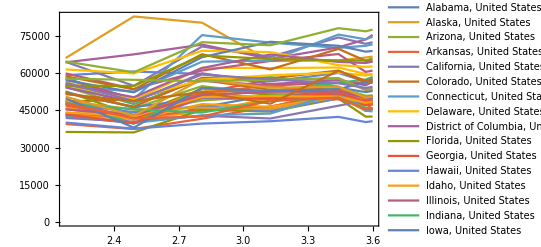

```mathematica
DateListPlot[Normal[ds[[All,"AverageTeacherSalaryConstantDollars"]]],PlotLegends->Normal[ds[[All,"State"]]]]
```

```mathematica
EntityList[EntityClass["AdministrativeDivision","USStatesMidwest"]]
```

{Illinois, United States,Indiana, United States,Iowa, United States,Kansas, United States,Michigan, United States,Minnesota, United States,Missouri, United States,Nebraska, United States,North Dakota, United States,Ohio, United States,South Dakota, United States,Wisconsin, United States}

```mathematica
Select[ds,MemberQ[EntityList[EntityClass["AdministrativeDivision","USStatesMidwest"]],#State]&]
```

Dataset[<>]

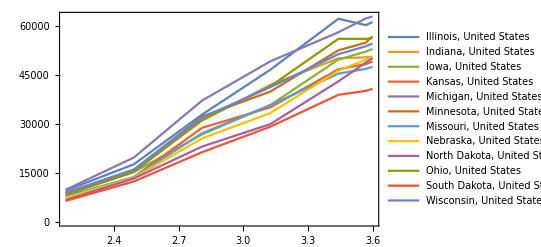

```mathematica
Module[{midwestst=Select[ds,MemberQ[EntityList[EntityClass["AdministrativeDivision","USStatesMidwest"]],#State]&]},
DateListPlot[midwestst[[All,"AverageTeacherSalaryCurrentDollars"]],PlotLegends->Normal@midwestst[[All,"State"]]]]
```

```mathematica
Partition[{{DateObject[{1969,1,1},"Day","Gregorian",-5.],Quantity["59 953.89", "USDollars"]},{DateObject[{1979,1,1},"Day","Gregorian",-5.],Quantity["53 659.23", "USDollars"]},{DateObject[{1989,1,1},"Day","Gregorian",-5.],Quantity["61 126.77", "USDollars"]},{DateObject[{1999,1,1},"Day","Gregorian",-5.],Quantity["64 989.30", "USDollars"]},{DateObject[{2009,1,1},"Day","Gregorian",-5.],Quantity["67 788.62", "USDollars"]},{DateObject[{2013,1,1},"Day","Gregorian",-5.],Quantity["60 561.73", "USDollars"]},{DateObject[{2014,1,1},"Day","Gregorian",-5.],Quantity["61 083.00", "USDollars"]}},2,1]
```

{{{Day: Wed 1 Jan 1969,59 953.89 $},{Day: Mon 1 Jan 1979,53 659.23 $}},{{Day: Mon 1 Jan 1979,53 659.23 $},{Day: Sun 1 Jan 1989,61 126.77 $}},{{Day: Sun 1 Jan 1989,61 126.77 $},{Day: Fri 1 Jan 1999,64 989.30 $}},{{Day: Fri 1 Jan 1999,64 989.30 $},{Day: Thu 1 Jan 2009,67 788.62 $}},{{Day: Thu 1 Jan 2009,67 788.62 $},{Day: Tue 1 Jan 2013,60 561.73 $}},{{Day: Tue 1 Jan 2013,60 561.73 $},{Day: Wed 1 Jan 2014,61 083.00 $}}}

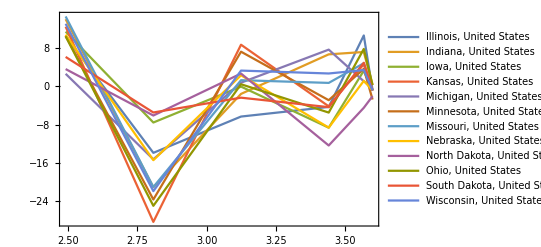

```mathematica
With[{data=#["State"] ->
TimeSeries@(Module[{date = First@Last@#,v1=Last@First@#,v2 = Last@Last@#},
{date,Quantity[((v1-v2)/v1) 100,"Percent"]}]&/@
Partition[ Normal[#["AverageTeacherSalaryConstantDollars"]],2,1]
)&/@Normal[Select[ds,MemberQ[EntityList[EntityClass["AdministrativeDivision","USStatesMidwest"]],#State]&]]},
DateListPlot[Last/@data,PlotLegends->First/@data]]
```

## put the Dataset into the cloud

```mathematica
CloudPut[ds]
```

CloudObject[]